the 1 half, Tmax = 191.846

The 2 half, Tmin = 188.971

the 3 half, Tmax = 200.29

The 4 half, Tmin = 196.889

the 5 half, Tmax = 207.684

The 6 half, Tmin = 203.767

the 7 half, Tmax = 214.057

The 8 half, Tmin = 209.652

the 9 half, Tmax = 219.473

The 10 half, Tmin = 214.62

the 11 half, Tmax = 224.015

The 12 half, Tmin = 218.763

the 13 half, Tmax = 227.783

The 14 half, Tmin = 222.181

the 15 half, Tmax = 230.877

The 16 half, Tmin = 224.976

the 17 half, Tmax = 233.397

The 18 half, Tmin = 227.245

the 19 half, Tmax = 235.435

The 20 half, Tmin = 229.074

the 21 half, Tmax = 237.074

The 22 half, Tmin = 230.541

the 23 half, Tmax = 238.386

The 24 half, Tmin = 231.713

the 25 half, Tmax = 239.432

The 26 half, Tmin = 232.647

the 27 half, Tmax = 240.264

The 28 half, Tmin = 233.388

the 29 half, Tmax = 240.924

The 30 half, Tmin = 233.975

the 31 half, Tmax = 241.446

The 32 half, Tmin = 234.439

the 33 half, Tmax = 241.858

The 34 half, Tmin = 234.805

the 35 half, Tmax = 242.184

The 36 half, Tmin = 235.094

the 37 half, Tmax = 242.441

The 38 half, Tmin = 235.322

the 39 half, Tmax = 242.643

The 40 half, Tmin = 235.502

the 41 half, Tmax = 242.802

The 42 half, Tmin = 235.643

the 43 half, Tmax = 242.927

The 44 half, Tmin = 235.754

the 45 half, Tmax = 243.026

The 46 half, Tmin = 235.842

the 47 half, Tmax = 243.104

The 48 half, Tmin = 235.911

the 49 half, Tmax = 243.164

The 50 half, Tmin = 235.965

the 51 half, Tmax = 243.212

The 52 half, Tmin = 236.007

the 53 half, Tmax = 243.25

The 54 half, Tmin = 236.041

the 55 half, Tmax = 243.28

The 56 half, Tmin = 236.067

the 57 half, Tmax = 243.303

The 58 half, Tmin = 236.087

the 59 half, Tmax = 243.321

The 60 half, Tmin = 236.104

the 61 half, Tmax = 243.336

The 62 half, Tmin = 236.116

the 63 half, Tmax = 243.347

The 64 half, Tmin = 236.126

the 65 half, Tmax = 243.356

The 66 half, Tmin = 236.134

the 67 half, Tmax = 243.363

The 68 half, Tmin = 236.14

the 69 half, Tmax = 243.368

The 70 half, Tmin = 236.145

the 71 half, Tmax = 243.373

The 72 half, Tmin = 236.149

the 73 half, Tmax = 243.376

The 74 half, Tmin = 236.152

the 75 half, Tmax = 243.379

The 76 half, Tmin = 236.154

the 77 half, Tmax = 243.381

The 78 half, Tmin = 236.156

the 79 half, Tmax = 243.382

The 80 half, Tmin = 236.158

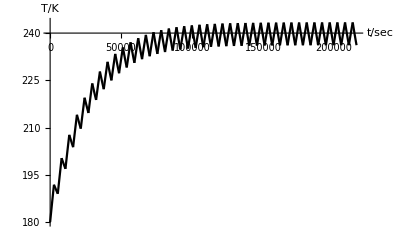

```mathematica
σ = 5.67*10^-8;
m=83.6;
c=900;
F=1500;
R=0.2925;
hour = 3/4;
T0 =180;
Tmin = T0;
n = 40;
p = Range[2*n];

For[i=0,i<n,i++,
solution1 = NDSolve[{-σ*T1[x]^4*4*Pi*R^2+Pi*R^2*F == c*m*T1'[x],T1[(2*i)*hour*3600]==Tmin},T1[x],{x,(2*i)*hour*3600,(2*i+1)*hour*3600}];
p[[2*i+1]] = Plot[Evaluate[T1[x]/.solution1],{x,(2*i)*hour*3600,(2*i+1)*hour*3600},PlotRange->All,PlotTheme->"Monochrome"];

x = (2*i+1)*hour*3600; 
Tmax = T1[x]/.solution1[[1]];
Print["the ",2*i+1, " half, Tmax = ",Tmax];

solution2 =  NDSolve[{-σ*T2[t]^4*4*Pi*R^2== c*m*T2'[t],T2[(2*i+1)*hour*3600]==Tmax},T2[t],{t,(2*i+1)*hour*3600,(2*i+2)*hour*3600}];

p[[2*i+2]] = Plot[Evaluate[T2[t]/.solution2],{t,(2*i+1)*hour*3600,(2*i+2)*hour*3600},PlotTheme->"Monochrome",PlotRange->All];

t = (2*i+2)*hour*3600; 
Tmin= T2[t]/.solution2[[1]];
Print["The ",2*i+2 ," half, Tmin = ",Tmin];

Clear[t,x,solution1,solution2];

]

Show[p,AxesOrigin->{0,240} ,AxesLabel->{"t/sec","T/K"}]

Clear["Global`*"]
```